```mathematica
χPDF[x0_?NumericQ,DI_?NumericQ,γ_?NumericQ]:=χPDF[x0,DI,γ]=(γ^(γ/DI)/Gamma[γ/DI,0,γ]) ⅇ^(-γ x0)x0^(γ/DI-1)(*UnitStep[1-x0]UnitStep[x0]*)
χIavg[DI_?NumericQ,γ_?NumericQ]:=χIavg[DI,γ]= (1/DI-(γ^(γ/DI-1)ⅇ^-γ)/Gamma[γ/DI,0,γ])
aλ[DI_?NumericQ,γ1_?NumericQ]:=aλ[DI,γ1]=DI/γ1 χPDF[1,DI,γ1]UnitStep[1-DI/γ1 χPDF[1,DI,γ1]]+UnitStep[DI/γ1 χPDF[1,DI,γ1]-1](*ⅇ^(-(1-χIavgN[DI,γ1,0,0])γ1)*)
aPET[DI_?NumericQ,γ1_?NumericQ]:=aPET[DI,γ1]=(1-χIavg[DI,γ1])(*(1-(ⅇ^(10(DI-1))/(1+ⅇ^(10(DI-1)))))*)

(**)
ξ1=2.0; (*3.5 Lower Number Lowers Curve*)
ξ2=2.0; (*4.1 Higher Number Lowers Curve*)
ξ3=.55;(*1.35*)
ξ4=3.0;
ϑ[LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=ϑ[LI,γs,β]=Max[-LI/(γs^(2(1-ξ1 β^2)))(ξ3+ξ4(β-β^2))+ⅇ^(-2(1-ξ2 β^2)LI/(γs^(1-.5 β^2))),0]
pχPlot[x_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=pχPlot[x,LI,γs,β,ϑ]=(*CC1N[LI,γs,β,ϑ] *)Exp[Evaluate[Max[Log[(1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))]+Log[(1-x)^((γs (1-ϑ))/(1-β ϑ))]-Log[(x^(1-γs/LI))]+Log[Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]]-Log[Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI]]-Log[Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ]],-700]]]
Clear[pq,pz,pχ]
(*Rainfall PDF, exponential and mixed exponential*)
pz[z_,γ_]:=γ ⅇ^(-γ z)UnitStep[z]
CC1[LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=CC1[LI,γs,β,ϑ]=Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]/(Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI])(1/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])
pχ[x_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=pχ[x,LI,γs,β,ϑ]=CC1[LI,γs,β,ϑ]((1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))(1-x)^((γs (1-ϑ))/(1-β ϑ)))/x^(1-γs/LI)
pq[q_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=pq[q,LI,γs,β]=NIntegrate[(((2+q+u^2 β-u (2+β+q β)+√(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2))/(2 √(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2)))pz[1/(2 (-1+u β))(-q+u β+q u β-u^2 β-√(-4 (q-q u) (-1+u β)+(q-u β-q u β+u^2 β)^2)),γs]pχ[u,LI,γs ,β,ϑ[LI,γs,β]]),{u,0,1},Method->{Automatic,"SymbolicProcessing"->0}]
```

```mathematica
LabelSize = 15;
```

```mathematica
(*https://mathematica.stackexchange.com/questions/144683/detecting-crossing-events-of-jumps-with-ndsolve*)
(*Parameters*)
λ=0.1;  (*Poisson rate for inter-arrival times*)
w = 100*10
μ = .05
w0 = μ w
w1=(1-μ)w;
α=2*10;
γ0=w0/α;  (*Exponential rate for rainfall marks*)
PET = .15*10
yr=1;   (*Time span in years*)

(*Hydro Parameters*)
β = .1
BI =.6

SeedRandom[1234]; (*Set the seed for reproducibility*)

(*Solve for soil moisture dynamics and capture events*)
{soilMoistureSol,eventData}=Reap[NDSolve[{ss'[t]==-PET/w0 ss[t],ss[0]==.7,tnext[0]==RandomReal[ExponentialDistribution[λ]],WhenEvent[t==tnext[t],{RR1=RandomReal[ExponentialDistribution[1/α]],y=RR1-(1-ss[t])*w0,If[ss[t]+RR1/w0>1,(*Sow time and excess series*)Sow[{{t,RR1},{t,y}}],(*Sow time and regular rainfall series*)Sow[{{t,RR1},{None,None}}]],ss[t]->Min[1,ss[t]+RR1/w0],,tnext[t]->t+RandomReal[ExponentialDistribution[λ]]}]},{ss,tnext},{t,0,365*yr},DiscreteVariables->{tnext}]];

(*Extract recorded times and rainfall marks*)
eventTimesAndMarks=Append[Prepend[Flatten[eventData,1][[All,1,All]],{0,0}],{365,0}];
spikeData=Flatten[Map[Function[event,With[{time=event[[1]],mark=event[[2]]},{{time,0},{time,mark},{time,0}}]],eventTimesAndMarks],1];

eventInfiltrationTimesAndMarks=Append[Prepend[Select[Flatten[eventData,1][[All,2,All]],Not[SameQ[#,{None,None}]]&],{0,0}],{365,0}];
spikeInfiltrationData=Flatten[Map[Function[event,With[{time=event[[1]],mark=event[[2]]},{{time,0},{time,mark},{time,0}}]],eventInfiltrationTimesAndMarks],1];

(*Extract the soil moisture function*)
soilMoisture=ss/. First[soilMoistureSol];

(*Create consistent plot size*)
plotSize=250*1.1;
plotfactor =1.25;

row1 = GraphicsRow[{

(*1. Realization of the marked Poisson process*)
ListPlot[spikeData,PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1]},Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Rain Amount, R̄, mm"},PlotLabel->"Rain Marked Poisson Process",ImageSize->plotSize*1.05,AspectRatio->1/2, Joined->True,Epilog->{Black,PointSize[Large],Style[Text["×",#,{0,-0.5}],Bold]&/@eventTimesAndMarks},PlotRange->All,LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)Show[Plot[PDF[ExponentialDistribution[1/α],100-x],{x,0,100},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{"","Rainfall PDF"},{None, None}},FrameTicks->None],PlotRange->{{0,100},{0,.05}},Ticks->None,ImageSize->plotSize/plotfactor,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&,
(*3. Realization of the soil moisture process*)
Plot[Evaluate[soilMoisture[t]],{t,0,365*yr},PlotRange->{0,1},PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1.4]},PlotLabel->"Upper Soil Layer Dynamics",Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Soil Moisture, (χ̄)_0"},ImageSize->plotSize*1,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]],
(*4. Gamma distribution rotated*)Show[Plot[χPDF[1-x,PET/(λ α),γ0],{x,0,1},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{"","Upper Soil PDF"},{None, None}},FrameTicks->None,LabelStyle->Directive[LabelSize ,Bold]],Ticks->None,ImageSize->plotSize/plotfactor]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&,
Spacer[250],
Spacer[150]},
Spacings->-10,ImageSize->1550]
```

1000

0.05

50.

1.5

0.1

0.6

-Graphics-

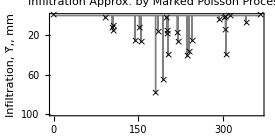

```mathematica
row2 = GraphicsRow[{Spacer[285],
Spacer[150],
(*1. Realization of the marked Poisson process*)
ListPlot[Map[{#[[1]],-#[[2]]}&,spikeInfiltrationData],(*Negate y-values*)PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1]},Frame->{{True,False},{True,False}},FrameLabel->{"Time (days)","Infiltration, Ȳ,, mm"},PlotRange->{0,-100},PlotLabel->"Infiltration Approx. by Marked Poisson Process",ImageSize->plotSize,AspectRatio->1/2,Joined->True,Epilog->{Black,PointSize[Large],Style[Text["×",{#[[1]],-#[[2]]},{0,-0.5}],Bold]&/@eventInfiltrationTimesAndMarks},PlotRange->All,FrameTicks->{Automatic,(*Customize y-axis ticks*)Table[{y,ToString[Abs[y]]},{y,-100,0,20}]},LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)
Show[Plot[PDF[ExponentialDistribution[1/α],x],{x,0,100},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{"","Infiltration PDF"},{None, None}},FrameTicks->None],PlotRange->{{0,100},{0,.055}},Ticks->None,ImageSize->plotSize/plotfactor*1,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&,
Spacer[295],
Spacer[150]},
Spacings->-45,ImageSize->1550]
```

```mathematica
Column[{row1,row2},Spacings->-5]
```

-Graphics-

```mathematica
Ft[x_,R_,w_,β_]:=(R(1-β x))/(w(1-x)+R (1-β x))
DI = PET/(λ α)
timeInfiltration =Select[Flatten[eventData,1][[All,2,All]],Not[SameQ[#,{None,None}]]&][[All,1]];
marksInfiltration = Select[Flatten[eventData,1][[All,2,All]],Not[SameQ[#,{None,None}]]&][[All,2]];
```

0.75

```mathematica
nMax=Length[timeInfiltration ];

{soilMoistureSol2,eventData3}=Reap[NDSolve[{ss'[t]==-(PET aPET[PET/(α λ),γ0]+BI)/w1 ss[t],ss[0]==.5, n1[0]==1,WhenEvent[t==timeInfiltration[[n1[t]]],{RR1=marksInfiltration[[n1[t]]],Sow[{t,RR1((Ft[ss[t],RR1,w1,β]+(1-Ft[ss[t],RR1,w1,β])β ss[t]))}],ss[t]->ss[t]+RR1/w1(1-(Ft[ss[t],RR1,w1,β]+(1-Ft[ss[t],RR1,w1,β])β ss[t])),n1[t]->If[n1[t]<nMax,n1[t]+1,n1[t]] (*Increment n*)}]},{ss,n1},{t,0,365 yr},DiscreteVariables->{n1}]]
```

Part::pkspec1: The expression n1[t] cannot be used as a part specification.

{{{ss→InterpolatingFunction[…],n1→InterpolatingFunction[…]}},{{{90.6487,0.119592},{103.816,0.814126},{104.655,1.16425},{104.783,0.68696},{144.373,2.34564},{151.896,0.961396},{154.358,2.643},{180.404,14.3483},{184.684,1.51348},{193.88,12.158},{198.722,0.206661},{200.384,1.68626},{201.023,2.06678},{202.067,6.77028},{218.945,2.19827},{219.935,3.96961},{235.968,7.87131},{239.573,7.05222},{244.52,4.48238},{293.198,0.40153},{302.658,0.23633},{302.969,0.17448},{304.182,1.87118},{305.032,8.56191},{312.507,0.0750689},{340.436,0.806337}}}}

```mathematica
(*Extract the soil moisture function*)
soilMoisture2=ss/. First[soilMoistureSol2];
CNsim = Table[25400./(w1(1-soilMoisture2[t])+254),{t,0,365 yr,.1}];
MinCN=MinCN=25400./(w1(1-0)+254);
(*Extract recorded times and rainfall marks*)
eventRunoffTimesAndMarks=Append[Prepend[Flatten[eventData3,1],{0,0}],{365,0}];
spikeRunoffData=Flatten[Map[Function[event,With[{time=event[[1]],mark=event[[2]]},{{time,0},{time,mark},{time,0}}]],eventRunoffTimesAndMarks],1];
```

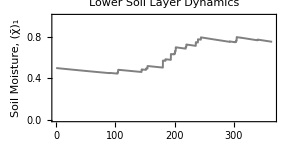

-Graphics-

```mathematica
row3 = GraphicsRow[{Spacer[235],
Spacer[150],
(*3. Realization of the soil moisture process*)
Plot[Evaluate[soilMoisture2[t]],{t,0,365*yr},PlotRange->{0,1},PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1.4]},PlotLabel->"Lower Soil Layer Dynamics",Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Soil Moisture, (χ̄)_1"},ImageSize->plotSize*1.05,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)
Show[Plot[pχPlot[1-x,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]],{x,0,1},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{None,"Lower Soil PDF"},{None, None}},FrameTicks->None],Ticks->None,ImageSize->plotSize/plotfactor*.95,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&,
Spacer[250],
Spacer[150]},
Spacings->-5,ImageSize->1550]

row4= GraphicsRow[{Spacer[255],
Spacer[150],
(*3. Realization of the soil moisture process*)
Plot[Evaluate[25400./(w1(1-soilMoisture2[t])+254)],{t,0,365*yr},PlotRange->{MinCN,60},PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1.4]},PlotLabel->"Curve Number Dynamics",Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Curve Number, CN"},ImageSize->plotSize*1.05,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)
Show[Plot[Evaluate[25400/(CN^2 w1)pχPlot[(-25400+CN (254+ w1))/(CN w1),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]/.{CN->60-CN1}],{CN1,0,60-MinCN},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{None,"Curve Number PDF"},{None, None}},FrameTicks->None],Ticks->None,ImageSize->plotSize/plotfactor*.9,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&,
(*Runoff Realizations*)
ListPlot[spikeRunoffData,PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1]},Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Runoff, Q̄, mm"},PlotLabel->"Event Runoff",ImageSize->plotSize*1.1,AspectRatio->1/2, Joined->True,Epilog->{Black,PointSize[Large],Style[Text["×",#,{0,-0.5}],Bold]&/@eventRunoffTimesAndMarks},PlotRange->{0,20},LabelStyle->Directive[LabelSize ,Bold]],
(**)
Show[Plot[aλ[DI,(w μ)/α](1/(w(1-μ))pq[(20-Q)/(w(1-μ)),Ceiling[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],3],(w (1-μ))/α,β ]),{Q,0,20},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{None,"Runoff PDF"},{None, None}},FrameTicks->None],PlotRange->{{0,20},{0,.2}},Ticks->None,ImageSize->plotSize/plotfactor*.9,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold],LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&},
Spacings->-15,ImageSize->1535]
```

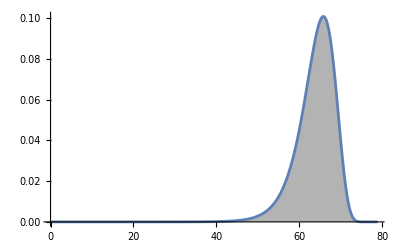

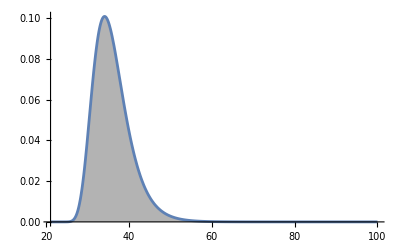

```mathematica
Plot[Evaluate[25400/(CN^2 w1)pχPlot[(-25400+CN (254+ w1))/(CN w1),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]/.{CN->100-CN1}],{CN1,0,100-MinCN},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotRange->All]
Plot[Evaluate[25400/(CN^2 w1)pχPlot[(-25400+CN (254+ w1))/(CN w1),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]],{CN,MinCN,100},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotRange->All]
```

```mathematica
Column[{Column[{row1,row2},Spacings->-7],
Column[{row3,row4},Spacings->-3.5]},Spacings->-6]
```

-Graphics-
-Graphics-

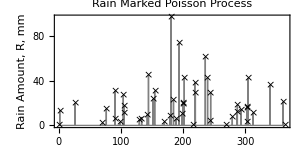

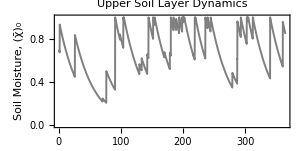

-Graphics-

-Graphics-

```mathematica
row11= GraphicsRow[{

(*1. Realization of the marked Poisson process*)
ListPlot[spikeData,PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1]},Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Rain Amount, R̄, mm"},PlotLabel->"Rain Marked Poisson Process",ImageSize->plotSize*1.1,AspectRatio->1/2, Joined->True,Epilog->{Black,PointSize[Large],Style[Text["×",#,{0,-0.5}],Bold]&/@eventTimesAndMarks},PlotRange->All,LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)Show[Plot[PDF[ExponentialDistribution[1/α],100-x],{x,0,100},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{"","Rainfall PDF"},{None, None}},FrameTicks->None],PlotRange->{{0,100},{0,.05}},Ticks->None,ImageSize->plotSize/plotfactor*.95,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&,
Spacer[250],
Spacer[150]},
Spacings->-10,ImageSize->1050]

row12= GraphicsRow[{
(*3. Realization of the soil moisture process*)
Plot[Evaluate[soilMoisture[t]],{t,0,365*yr},PlotRange->{0,1},PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1.4]},PlotLabel->"Upper Soil Layer Dynamics",Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Soil Moisture, (χ̄)_0"},ImageSize->plotSize*1.1,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]],
(*4. Gamma distribution rotated*)Show[Plot[χPDF[1-x,PET/(λ α),γ0],{x,0,1},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{"","Upper Soil PDF"},{None, None}},FrameTicks->None,LabelStyle->Directive[LabelSize ,Bold]],Ticks->None,ImageSize->plotSize/plotfactor*.95]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&,
Spacer[250],
Spacer[150]},
Spacings->-10,ImageSize->1050]

row21 = GraphicsRow[{
(*1. Realization of the marked Poisson process*)
ListPlot[Map[{#[[1]],-#[[2]]}&,spikeInfiltrationData],(*Negate y-values*)PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1]},Frame->{{True,False},{True,False}},FrameLabel->{"Time (days)","Infiltration, Ȳ, mm"},PlotRange->{0,-100},PlotLabel->"Infiltration Approx. by Marked Poisson Process",ImageSize->plotSize*1.27,AspectRatio->1/2,Joined->True,Epilog->{Black,PointSize[Large],Style[Text["×",{#[[1]],-#[[2]]},{0,-0.5}],Bold]&/@eventInfiltrationTimesAndMarks},PlotRange->All,FrameTicks->{Automatic,(*Customize y-axis ticks*)Table[{y,ToString[Abs[y]]},{y,-100,0,20}]},LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)
Show[Plot[PDF[ExponentialDistribution[1/α],x],{x,0,100},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{"","Infiltration PDF"},{None, None}},FrameTicks->None],PlotRange->{{0,100},{0,.055}},Ticks->None,ImageSize->plotSize/plotfactor*1,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&,
(*Runoff Realizations*)
ListPlot[spikeRunoffData,PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1]},Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Runoff, Q̄, mm"},PlotLabel->"Event Runoff",ImageSize->plotSize*1.2,AspectRatio->1/2, Joined->True,Epilog->{Black,PointSize[Large],Style[Text["×",#,{0,-0.5}],Bold]&/@eventRunoffTimesAndMarks},PlotRange->{0,20},LabelStyle->Directive[LabelSize ,Bold]],
(**)
Show[Plot[aλ[DI,(w μ)/α](1/(w(1-μ))pq[(20-Q)/(w(1-μ)),Ceiling[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],3],(w (1-μ))/α,β ]),{Q,0,20},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{None,"Runoff PDF"},{None, None}},FrameTicks->None],PlotRange->{{0,20},{0,.2}},Ticks->None,ImageSize->plotSize/plotfactor*.9,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold],LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&},
Spacings->{{-5,-15,15,-2},0},ImageSize->1050]

row31 = GraphicsRow[{
(*3. Realization of the soil moisture process*)
Plot[Evaluate[soilMoisture2[t]],{t,0,365*yr},PlotRange->{0,1},PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1.4]},PlotLabel->"Lower Soil Layer Dynamics",Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Soil Moisture, (χ̄)_1"},ImageSize->plotSize*1.,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)
Show[Plot[pχPlot[1-x,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]],{x,0,1},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{None,"Lower Soil PDF"},{None, None}},FrameTicks->None],Ticks->None,ImageSize->plotSize/plotfactor*.85,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&,
Plot[Evaluate[25400./(w1(1-soilMoisture2[t])+254)],{t,0,365*yr},PlotRange->{MinCN,60},PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1.4]},PlotLabel->"Curve Number Dynamics",Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Curve Number, CN"},ImageSize->plotSize*1.,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)
Show[Plot[Evaluate[25400/(CN^2 w1)pχPlot[(-25400+CN (254+ w1))/(CN w1),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]/.{CN->60-CN1}],{CN1,0,60-MinCN},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{None,"Curve Number PDF"},{None, None}},FrameTicks->None],Ticks->None,ImageSize->plotSize/plotfactor*.85,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&},
Spacings->{{-5,-5,-10,-27},0},ImageSize->1050]
```

```mathematica
row31 = GraphicsRow[{
(*3. Realization of the soil moisture process*)
Plot[Evaluate[soilMoisture2[t]],{t,0,365*yr},PlotRange->{0,1},PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1.4]},PlotLabel->"Lower Soil Layer Dynamics",Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Soil Moisture, (χ̄)_1"},ImageSize->plotSize*1.15,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)
Show[Plot[pχPlot[1-x,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]],{x,0,1},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{None,"Lower Soil PDF"},{None, None}},FrameTicks->None],Ticks->None,ImageSize->plotSize/plotfactor*.95,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&,
Plot[Evaluate[25400./(w1(1-soilMoisture2[t])+254)],{t,0,365*yr},PlotRange->{MinCN,60},PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1.4]},PlotLabel->"Curve Number Dynamics",Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Curve Number, CN"},ImageSize->plotSize*1.15,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)
Show[Plot[Evaluate[25400/(CN^2 w1)pχPlot[(-25400+CN (254+ w1))/(CN w1),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]/.{CN->60-CN1}],{CN1,0,60-MinCN},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{None,"Curve Number PDF"},{None, None}},FrameTicks->None],Ticks->None,ImageSize->plotSize/plotfactor*.95,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&},
Spacings->{{-5,-5,-1,-20},0},ImageSize->1100]
```

-Graphics-

```mathematica
export1 = Column[{Column[{row11,row12},Spacings->-3.5],
Column[{row21,row31},Spacings->-1]},Spacings->-2.5]
```

-Graphics-
-Graphics-

```mathematica
row11= GraphicsRow[{

(*1. Realization of the marked Poisson process*)
ListPlot[spikeData,PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1]},Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Rain Amount, R̄, mm"},PlotLabel->"Rain Marked Poisson Process",ImageSize->plotSize*1.1,AspectRatio->1/2, Joined->True,Epilog->{Black,PointSize[Large],Style[Text["×",#,{0,-0.5}],Bold]&/@eventTimesAndMarks},PlotRange->All,LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)Show[Plot[PDF[ExponentialDistribution[1/α],100-x],{x,0,100},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{"","Rainfall PDF"},{None, None}},FrameTicks->None],PlotRange->{{0,100},{0,.05}},Ticks->None,ImageSize->plotSize/plotfactor*.95,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&},
Spacings->-15,ImageSize->525];

row12= GraphicsRow[{
(*3. Realization of the soil moisture process*)
Plot[Evaluate[soilMoisture[t]],{t,0,365*yr},PlotRange->{0,1},PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1.4]},PlotLabel->"Upper Soil Layer Dynamics",Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Soil Moisture, (χ̄)_0"},ImageSize->plotSize*1.1,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]],
(*4. Gamma distribution rotated*)Show[Plot[χPDF[1-x,PET/(λ α),γ0],{x,0,1},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{"","Upper Soil PDF"},{None, None}},FrameTicks->None,LabelStyle->Directive[LabelSize ,Bold]],Ticks->None,ImageSize->plotSize/plotfactor*.95]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&},
Spacings->-10,ImageSize->535];

row211 = GraphicsRow[{
(*1. Realization of the marked Poisson process*)
ListPlot[Map[{#[[1]],-#[[2]]}&,spikeInfiltrationData],(*Negate y-values*)PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1]},Frame->{{True,False},{True,False}},FrameLabel->{"Time (days)","Infiltration, Ȳ, mm"},PlotRange->{0,-100},PlotLabel->"Infiltration Approx. by Marked Poisson Process",ImageSize->plotSize*1.38,AspectRatio->1/2,Joined->True,Epilog->{Black,PointSize[Large],Style[Text["×",{#[[1]],-#[[2]]},{0,-0.5}],Bold]&/@eventInfiltrationTimesAndMarks},PlotRange->All,FrameTicks->{Automatic,(*Customize y-axis ticks*)Table[{y,ToString[Abs[y]]},{y,-100,0,20}]},LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)
Show[Plot[PDF[ExponentialDistribution[1/α],x],{x,0,100},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{"","Infiltration PDF"},{None, None}},FrameTicks->None],PlotRange->{{0,100},{0,.055}},Ticks->None,ImageSize->plotSize/plotfactor*1,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&},
Spacings->{{0,-50},0},ImageSize->535];
row212 = GraphicsRow[{
(*Runoff Realizations*)
ListPlot[spikeRunoffData,PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1]},Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Runoff, Q̄, mm"},PlotLabel->"Event Runoff",ImageSize->plotSize*1.2,AspectRatio->1/2, Joined->True,Epilog->{Black,PointSize[Large],Style[Text["×",#,{0,-0.5}],Bold]&/@eventRunoffTimesAndMarks},PlotRange->{0,20},LabelStyle->Directive[LabelSize ,Bold]],
(**)
Show[Plot[aλ[DI,(w μ)/α](1/(w(1-μ))pq[(20-Q)/(w(1-μ)),Ceiling[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],3],(w (1-μ))/α,β ]),{Q,0,20},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{None,"Runoff PDF"},{None, None}},FrameTicks->None],PlotRange->{{0,20},{0,.2}},Ticks->None,ImageSize->plotSize/plotfactor*.9,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold],LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&},
Spacings->{{-2,-10},0},ImageSize->520];

row311 = GraphicsRow[{
(*3. Realization of the soil moisture process*)
Plot[Evaluate[soilMoisture2[t]],{t,0,365*yr},PlotRange->{0,1},PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1.4]},PlotLabel->"Lower Soil Layer Dynamics",Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Soil Moisture, (χ̄)_1"},ImageSize->plotSize*1.15,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)
Show[Plot[pχPlot[1-x,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]],{x,0,1},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{None,"Lower Soil PDF"},{None, None}},FrameTicks->None],Ticks->None,ImageSize->plotSize/plotfactor*.95,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&},
Spacings->{{0,-5},0},ImageSize->545];

row312 = GraphicsRow[{
Plot[Evaluate[25400./(w1(1-soilMoisture2[t])+254)],{t,0,365*yr},PlotRange->{MinCN,60},PlotStyle->{Thick,GrayLevel[0.5],AbsoluteThickness[1.4]},PlotLabel->"Curve Number Dynamics",Frame->{{True, False},{True,False}},FrameLabel->{"Time (days)","Curve Number, CN"},ImageSize->plotSize*1.15,AspectRatio->1/2,LabelStyle->Directive[LabelSize ,Bold]],
(*2. Exponential distribution rotated*)
Show[Plot[Evaluate[25400/(CN^2 w1)pχPlot[(-25400+CN (254+ w1))/(CN w1),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]/.{CN->60-CN1}],{CN1,0,60-MinCN},Filling->Axis,FillingStyle->GrayLevel[0.7],PlotStyle->{Thick,GrayLevel[0.5]},Frame->{{True, True},{True,False}},PlotRange->All,FrameLabel->{{None,"Curve Number PDF"},{None, None}},FrameTicks->None],Ticks->None,ImageSize->plotSize/plotfactor*.95,LabelStyle->Directive[LabelSize ,Bold]]/. Graphics[primitives_,opts___]:>Graphics[primitives,opts]//Rotate[#,270 Degree]&},
Spacings->{{5,-15},0},ImageSize->560];
```

```mathematica
export11= Column[{Column[{row11,row12,row211},Spacings->-2.5],
Column[{row311,row212,row312},Spacings->0]},Spacings->-1.5]
```

-Graphics-
-Graphics-

```mathematica
Export["Figure2.pdf",export11]
```

Fig.X.1a.pdf